### Definitions

```mathematica
Np =5;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(-1/4))/lm;
$Assumptions = -1<k && Im[k]==0
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
```

-1<k&&Im[k]==0

### Coefficients from Analytical Calculation

```mathematica
p00int[a_, b_] := (a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) (128 a^6-1920 a^5 b+11376 a^4 b^2-33760 a^3 b^3+52896 a^2 b^4-42480 a b^5+14165 b^6))/(128 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^3 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))
p11int[a_,b_]:=(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) (2048 a^10-51200 a^9 b+552448 a^8 b^2-3368960 a^7 b^3+12790144 a^6 b^4-31468160 a^5 b^5+50808160 a^4 b^6-53441600 a^3 b^7+35386156 a^2 b^8-13510780 a b^9+2531379 b^10))/(2048 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^5 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))


p22int[a_,b_]:=(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^2 (16384 a^12-491520 a^11 b+6961152 a^10 b^2-61388800 a^9 b^3+369365760 a^8 b^4-1558195200 a^7 b^5+4607796480 a^6 b^6-9440467200 a^5 b^7+13199921280 a^4 b^8-12430412800 a^3 b^9+7709546856 a^2 b^10-2749574280 a b^11+642462133 b^12))/(131072 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^7 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))
p33int[a_,b_]:=(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^4 (5013504 a^14-175472640 a^13 b+2751537152 a^12 b^2-25517506560 a^11 b^3+155821338624 a^10 b^4-661582745600 a^9 b^5+2016692858880 a^8 b^6-4508822937600 a^7 b^7+7496276208960 a^6 b^8-9293003294400 a^5 b^9+8478172943856 a^4 b^10-5563850838560 a^3 b^11+2543935893828 a^2 b^12-694320487140 a b^13+128980250171 b^14))/(2097152 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^9 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))
p44int[a_,b_]:=6*(5 a^2 b^6 (20480 a^14-573440 a^13 b+7381780 a^12 b^2-57887200 a^11 b^3+308419825 a^10 b^4-1177022420 a^9 b^5+3301650254 a^8 b^6-6876931424 a^7 b^7+10638473440 a^6 b^8-12145693056 a^5 b^9+10110024960 a^4 b^10-5995573248 a^3 b^11+2412418176 a^2 b^12-616960512 a b^13+106801920 b^14))/(196608 (a-3 b)^(17/2) √((a (a-2 b))/(a-b)) (a-b)^(21/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

p55int[a_,b_]:=6*(7 √((a (a-2 b))/(a-b)) b^8 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (70000 a^16-2240000 a^15 b+33815908 a^14 b^2-319645424 a^13 b^3+2111381251 a^12 b^4-10278421832 a^11 b^5+37878905848 a^10 b^6-106980595232 a^9 b^7+232326714856 a^8 b^8-386927766144 a^7 b^9+490757682048 a^6 b^10-469089172992 a^5 b^11+332847093888 a^4 b^12-170781041664 a^3 b^13+60226845696 a^2 b^14-13765496832 a b^15+2162654208 b^16))/(786432 a^2 (a-3 b)^(23/2) (a-b)^(25/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p66int[a_,b_]:=6*(7 √((a (a-2 b))/(a-b)) b^10 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (435456 a^18-15676416 a^17 b+272391924 a^16 b^2-3031228032 a^15 b^3+24078957777 a^14 b^4-143844526812 a^13 b^5+663857700870 a^12 b^6-2399943912912 a^11 b^7+6838907811192 a^10 b^8-15379009683168 a^9 b^9+27214669306128 a^8 b^10-37664153038080 a^7 b^11+40395367337088 a^6 b^12-33170049965568 a^5 b^13+20502998081792 a^4 b^14-9271265486848 a^3 b^15+2913360638976 a^2 b^16-603288211456 a b^17+86108657664 b^18))/(4194304 a^2 (a-3 b)^(27/2) (a-b)^(29/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p77int[a_,b_]:=(11 a^2 b^12 (1267728 a^20-50709120 a^19 b+998794236 a^18 b^2-12833233776 a^17 b^3+119607983253 a^16 b^4-850483633824 a^15 b^5+4738548188616 a^14 b^6-21001211445984 a^13 b^7+74676898669296 a^12 b^8-213949274546304 a^11 b^9+494270740852416 a^10 b^10-918686229652224 a^9 b^11+1366757733444736 a^8 b^12-1614859880310784 a^7 b^13+1499572077065216 a^6 b^14-1079907836342272 a^5 b^15+592041296398336 a^4 b^16-239700850196480 a^3 b^17+68091055644672 a^2 b^18-12929219592192 a b^19+1687516692480 b^20))/(16777216 (a-3 b)^(29/2) √((a (a-2 b))/(a-b)) (a-b)^(33/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p88int[a_,b_]:=0.0001*a
```

```mathematica
p0upi[a_,b_]:=(2 a^(3/2) √((a (a-5 b))/(a-4 b)) (4 a^2-20 a b+13 b^2))/((a-4 b) ((2 a^2-9 a b+2 b^2)/(a-4 b))^(3/2) ((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2))^(3/2))
p1upi[a_,b_]:=(4 √a √((a (a-5 b))/(a-4 b)) (8 a^4-80 a^3 b+230 a^2 b^2-150 a b^3+51 b^4))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^2 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p2upi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^2 (208 a^4-2080 a^3 b+5704 a^2 b^2-2520 a b^3+1041 b^4))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^3 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p3upi[a_,b_]:=(2 √a √((a (a-5 b))/(a-4 b)) b^2 (96 a^6-1440 a^5 b+8544 a^4 b^2-25440 a^3 b^3+35950 a^2 b^4-11750 a b^5+4057 b^6))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^4 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p4upi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^4 (10944 a^6-164160 a^5 b+927632 a^4 b^2-2436320 a^3 b^3+2824052 a^2 b^4-766260 a b^5+251199 b^6))/(4 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^5 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p5upi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^4 (1920 a^8-38400 a^7 b+365280 a^6 b^2-2119200 a^5 b^3+7535480 a^4 b^4-15054800 a^3 b^5+14151074 a^2 b^6-3320370 a b^7+1013373 b^8))/(2 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^6 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p6upi[a_,b_]:=(7 √a √((a (a-5 b))/(a-4 b)) b^6 (24320 a^8-486400 a^7 b+4198400 a^6 b^2-20416000 a^5 b^3+59520992 a^4 b^4-99209920 a^3 b^5+79349280 a^2 b^6-16622400 a b^7+4759899 b^8))/(8 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^7 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p7upi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^6 (17920 a^10-448000 a^9 b+5958400 a^8 b^2-51968000 a^7 b^3+300480320 a^6 b^4-1136004800 a^5 b^5+2731897728 a^4 b^6-3878777280 a^3 b^7+2699928534 a^2 b^8-515426670 a b^9+138885561 b^10))/(4 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^8 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p8upi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^8 (8637440 a^10-215936000 a^9 b+2512321280 a^8 b^2-17856025600 a^7 b^3+84049420672 a^6 b^4-265171070080 a^5 b^5+545165914848 a^4 b^6-674883228480 a^3 b^7+416536368540 a^2 b^8-73561286700 a b^9+18714751479 b^10))/(64 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^9 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
```

```mathematica
p0downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) (32 a^4-320 a^3 b+980 a^2 b^2-900 a b^3+291 b^4))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^2 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p1downi[a_,b_]:=(4 √a √((a (a-5 b))/(a-4 b)) (32 a^6-480 a^5 b+2640 a^4 b^2-6400 a^3 b^3+6534 a^2 b^4-2670 a b^5+591 b^6))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^3 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p2downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) (1024 a^8-20480 a^7 b+161664 a^6 b^2-632960 a^5 b^3+1275568 a^4 b^4-1315680 a^3 b^5+814560 a^2 b^6-226800 a b^7+38787 b^8))/(2 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^4 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p3downi[a_,b_]:=(2 √a √((a (a-5 b))/(a-4 b)) b^2 (1920 a^8-38400 a^7 b+298272 a^6 b^2-1114080 a^5 b^3+2012056 a^4 b^4-1700560 a^3 b^5+1093126 a^2 b^6-258630 a b^7+53937 b^8))/(√((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^5 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p4downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^2 (49152 a^10-1228800 a^9 b+12996096 a^8 b^2-75601920 a^7 b^3+262431424 a^6 b^4-546903360 a^5 b^5+646586256 a^4 b^6-404622560 a^3 b^7+201602004 a^2 b^8-39328020 a b^9+7154793 b^10))/(8 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^6 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p5downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^4 (192000 a^10-4800000 a^9 b+50099200 a^8 b^2-281984000 a^7 b^3+921358080 a^6 b^4-1746771200 a^5 b^5+1815446896 a^4 b^6-985668960 a^3 b^7+455395410 a^2 b^8-78115050 a b^9+14059593 b^10))/(2 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^7 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p6downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^4 (737280 a^12-22118400 a^11 b+303585280 a^10 b^2-2520832000 a^9 b^3+13899984640 a^8 b^4-51938892800 a^7 b^5+128532250112 a^6 b^6-198914631680 a^5 b^7+175532339040 a^4 b^8-83323070400 a^3 b^9+34826787624 a^2 b^10-5336358120 a b^11+922043151 b^12))/(16 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^8 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p7downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^6 (4372480 a^12-131174400 a^11 b+1737684480 a^10 b^2-13381312000 a^9 b^3+66110564352 a^8 b^4-216838487040 a^7 b^5+468649408192 a^6 b^6-636717506880 a^5 b^7+497754487224 a^4 b^8-213045552240 a^3 b^9+82169950590 a^2 b^10-11460649950 a b^11+1913269401 b^12))/(4 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^9 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
p8downi[a_,b_]:=(√a √((a (a-5 b))/(a-4 b)) b^6 (36700160 a^14-1284505600 a^13 b+22022676480 a^12 b^2-243215974400 a^11 b^3+1878542310400 a^10 b^4-10360344960000 a^9 b^5+40708952695040 a^8 b^6-112217933900800 a^7 b^7+210179404583808 a^6 b^8-252285772437120 a^5 b^9+176873679573504 a^4 b^10-69279746855040 a^3 b^11+24805927380204 a^2 b^12-3189563413020 a b^13+514208228553 b^14))/(128 √((2 a^2-9 a b+2 b^2)/(a-4 b)) (4 a^2-20 a b+9 b^2)^10 √((a (4 a^2-20 a b+9 b^2))/(2 a^2-9 a b+2 b^2)))
```

```mathematica
p0up[k_]:=p0upi[A[lp[k]], B[1,lp[k],Np]]-p00int[A[lp[k]], B[1,lp[k],Np]]
p1up[k_]:=p1upi[A[lp[k]], B[1,lp[k],Np]]-p11int[A[lp[k]], B[1,lp[k],Np]]
p2up[k_]:=p2upi[A[lp[k]], B[1,lp[k],Np]]-p22int[A[lp[k]], B[1,lp[k],Np]]
p3up[k_]:=p3upi[A[lp[k]], B[1,lp[k],Np]]-p33int[A[lp[k]], B[1,lp[k],Np]]
p4up[k_]:=p4upi[A[lp[k]], B[1,lp[k],Np]]-p44int[A[lp[k]], B[1,lp[k],Np]]
p5up[k_]:=p5upi[A[lp[k]], B[1,lp[k],Np]]-p55int[A[lp[k]], B[1,lp[k],Np]]
p6up[k_]:=p6upi[A[lp[k]], B[1,lp[k],Np]]-p66int[A[lp[k]], B[1,lp[k],Np]]
p7up[k_]:=p7upi[A[lp[k]], B[1,lp[k],Np]]-p77int[A[lp[k]], B[1,lp[k],Np]]
p8up[k_]:=p8upi[A[lp[k]], B[1,lp[k],Np]]-p88int[A[lp[k]], B[1,lp[k],Np]]
```

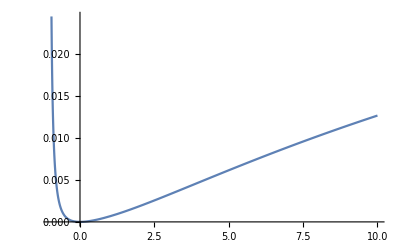

```mathematica
Plot[p22int[A[lp[k]], B[1,lp[k],Np]], {k,-0.99,10}]
```

```mathematica
p0down[k_]:=p0downi[A[lp[k]], B[1,lp[k],Np]]-p00int[A[lp[k]], B[1,lp[k],Np]]
p1down[k_]:=p1downi[A[lp[k]], B[1,lp[k],Np]]-p11int[A[lp[k]], B[1,lp[k],Np]]
p2down[k_]:=p2downi[A[lp[k]], B[1,lp[k],Np]]-p22int[A[lp[k]], B[1,lp[k],Np]]
p3down[k_]:=p3downi[A[lp[k]], B[1,lp[k],Np]]-p33int[A[lp[k]], B[1,lp[k],Np]]
p4down[k_]:=p4downi[A[lp[k]], B[1,lp[k],Np]]-p44int[A[lp[k]], B[1,lp[k],Np]]
p5down[k_]:=p5downi[A[lp[k]], B[1,lp[k],Np]]-p55int[A[lp[k]], B[1,lp[k],Np]]
p6down[k_]:=p6downi[A[lp[k]], B[1,lp[k],Np]]-p66int[A[lp[k]], B[1,lp[k],Np]]
p7down[k_]:=p7downi[A[lp[k]], B[1,lp[k],Np]]-p77int[A[lp[k]], B[1,lp[k],Np]]
p8down[k_]:=p8downi[A[lp[k]], B[1,lp[k],Np]]-p88int[A[lp[k]], B[1,lp[k],Np]]
```

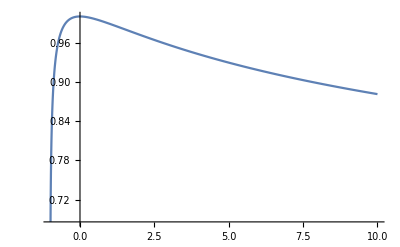

```mathematica
Plot[p2down[k], {k,-0.99,10}]
```

```mathematica
p0updown[k_]:= p00int[A[lp[k]], B[1,lp[k],Np]]
p1updown[k_]:= p11int[A[lp[k]], B[1,lp[k],Np]]
p2updown[k_]:= p22int[A[lp[k]], B[1,lp[k],Np]]
p3updown[k_]:= p33int[A[lp[k]], B[1,lp[k],Np]]
p4updown[k_]:= p44int[A[lp[k]], B[1,lp[k],Np]]
p5updown[k_]:= p55int[A[lp[k]], B[1,lp[k],Np]]
p6updown[k_]:= p66int[A[lp[k]], B[1,lp[k],Np]]
p7updown[k_]:= p77int[A[lp[k]], B[1,lp[k],Np]]
p8updown[k_]:= p88int[A[lp[k]], B[1,lp[k],Np]]

p0vac[k_]:= 1-p0up[k]-p0down[k]-p0updown[k]
p1vac[k_]:= 1-p1up[k]-p1down[k]-p1updown[k]
p2vac[k_]:= 1-p2up[k]-p2down[k]-p2updown[k]
p3vac[k_]:= 1-p3up[k]-p3down[k]-p3updown[k]
p4vac[k_]:= 1-p4up[k]-p4down[k]-p4updown[k]
p5vac[k_]:= 1-p5up[k]-p5down[k]-p5updown[k]
p6vac[k_]:= 1-p6up[k]-p6down[k]-p6updown[k]
p7vac[k_]:= 1-p7up[k]-p7down[k]-p7updown[k]
p8vac[k_]:= 1-p8up[k]-p8down[k]-p8updown[k]
```

## Null

```mathematica
acc = 20
```

20

```mathematica
s[i_]:=If[i==0,0,-i*Log[i]]
logc[i_]:=If[i≤10^(-acc),0,Log[i]]
```

```mathematica
q0[k_] := {p0vac[k], p1vac[k], p2vac[k], p3vac[k], p4vac[k], p5vac[k], p6vac[k], p7vac[k],p8vac[k]}
q1[k_] :={p0up[k], p1up[k], p2up[k], p3up[k], p4up[k], p5up[k], p6up[k],p7up[k], p8up[k]}
q2[k_] :={p0down[k], p1down[k], p2down[k], p3down[k], p4down[k], p5down[k], p6down[k],p7down[k], p8down[k]}
q3[k_] :={p0updown[k], p1updown[k], p2updown[k], p3updown[k], p4updown[k], p5updown[k], p6updown[k],p7updown[k], p8updown[k]}
```

```mathematica
q0[0.9]
```

{7.67569×10^-8,0.000071109,0.00308815,0.990887,0.996865,0.999948,0.999993,1.,1.00007}

```mathematica
(*without SSR*)
e[k_, i_] := s[q0[k][[i+1]]]+s[q1[k][[i+1]]]+s[q2[k][[i+1]]]+s[q3[k][[i+1]]]
i[k_,i_]:= 2*e[k,i]
```

```mathematica
(*with PSSR*)
ip[k_, m_] := 2*e[k,m]-s[(q0[k][[m+1]]+q3[k][[m+1]])] -s[(q1[k][[m+1]]+q2[k][[m+1]])]
ep[k_, m_] := e[k,m]-s[(q1[k][[m+1]]+q2[k][[m+1]])]-s[(q0[k][[m+1]]+q3[k][[m+1]])]
(*with NSSR*)
in[k_, m_] := 2*e[k,m]-s[q0[k][[m+1]]]-s[(q1[k][[m+1]]+q2[k][[m+1]])]-s[q3[k][[m+1]]]
en[k_, m_] := -s[(q1[k][[m+1]]+q2[k][[m+1]])]+s[ q1[k][[m+1]]]+s[q2[k][[m+1]]]
```

```mathematica
export[dataset_,label_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/"<>ToString[label],dataset, "CSV"]
```

```mathematica
(*export[Flatten[Table[ip[k,2], {k,-0.99,-0.01,0.01}]], ipmode2neg]*)
```

```mathematica
"/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/ipmode2neg"
```

/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/ipmode2neg

```mathematica
kappalogrange[i_]:= If[i≤0, i, 10^(i-1)]
eexpneg[i_]:=export[Flatten[Table[ep[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "emode"<>ToString[i]"neg"]
eexppos[i_]:=export[Flatten[Table[ep[k,i]/e[k,i], {k,0.01,5,0.01}]], "emode"<>ToString[i]"neg"]
epeexpneg[i_]:=export[Flatten[Table[ep[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "epemode"<>ToString[i]"neg"]
eneexpneg[i_]:=export[Flatten[Table[en[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "enemode"<>ToString[i]"neg"]
epeexppos[i_]:=export[Flatten[Table[ep[kappalogrange[k],i]/e[kappalogrange[k],i], {k,0.01,5,0.01}]], "epemode"<>ToString[i]"pos"]
eneexppos[i_]:=export[Flatten[Table[en[kappalogrange[k],i]/e[kappalogrange[k],i], {k,0.01,5,0.01}]], "enemode"<>ToString[i]"pos"]
```

```mathematica
(*
Table[epeexpneg[i], {i,0,3}]
Table[eneexpneg[i], {i,0,3}]*)
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode0 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode1 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode2 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode3 neg}

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode0 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode1 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode2 neg,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode3 neg}

```mathematica
(*Table[epeexppos[i], {i,0,3}]
Table[eneexppos[i], {i,0,3}]*)
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode0 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode1 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode2 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/epemode3 pos}

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode0 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode1 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode2 pos,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN5d1_1mode /data_ferm_5d1_mode/enemode3 pos}

```mathematica
Plot[(en[kappalogrange[j],2]), {j,-0.99,5},PlotRange->Full]
```

-Graphics-

```mathematica
Rasterize[%331,"Image"]
```

-Graphics-

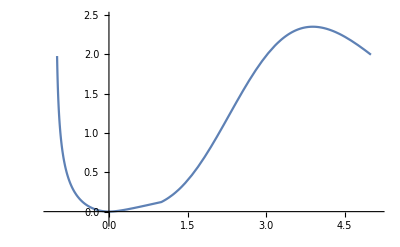

-Graphics-

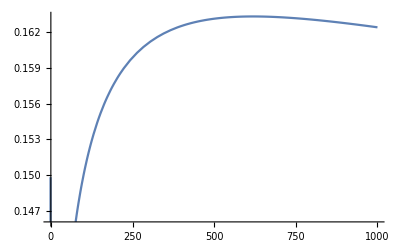

0

```mathematica
Plot[(en[k,1])/(e[k,1]), {k,-0.99,1000}]
en[0,1]
```

```mathematica
Plot[(en[k,2])/(e[k,2]), {k,-0.99,1000}]
```

-Graphics-

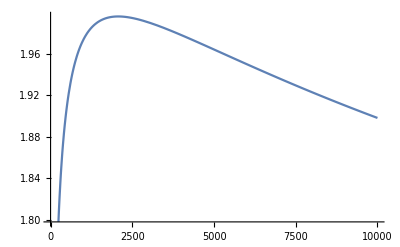

```mathematica
Plot[(i[k,3]), {k,-0.99,10000}]
```

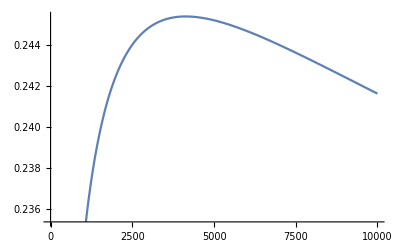

```mathematica
Plot[(en[k,4])/(e[k,4]), {k,-0.99,10000}]
```

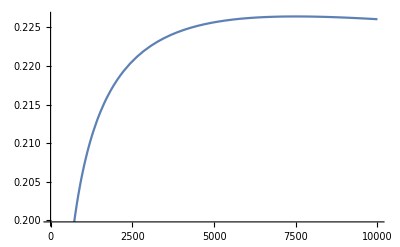

```mathematica
Plot[(en[k,5])/(e[k,5]), {k,-0.99,10000}]
```

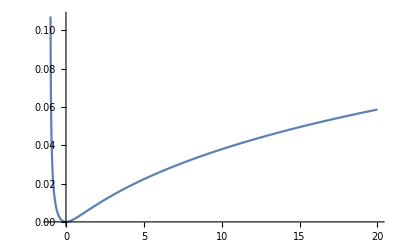

```mathematica
Plot[(en[k,6])/(e[k,6]), {k,-0.99,20}]
```

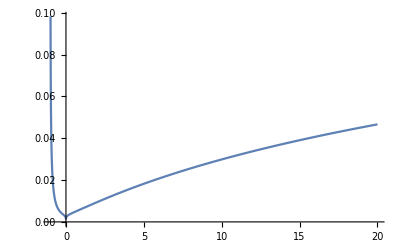

```mathematica
Plot[(en[k,7])/(e[k,7]), {k,-0.99,20}]
```

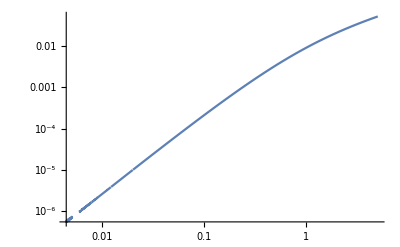

```mathematica
LogLogPlot[(ep[k,0])/(e[k,0]), {k,-0.99,5}]
```

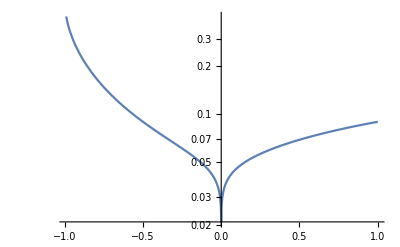

```mathematica
LogPlot[(ep[k,1])/(e[k,1]), {k,-0.99,1}]
```

```mathematica
LogPlot[(ep[kappalogrange[k],2])/(e[kappalogrange[k],2]), {k,-0.99,7}]
```

-Graphics-

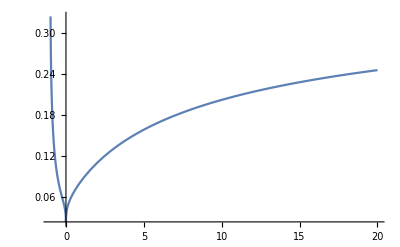

```mathematica
Plot[(ep[k,3])/(e[k,3]), {k,-0.99,20}]
```

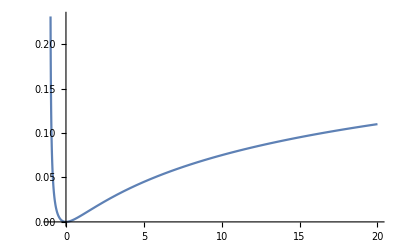

```mathematica
Plot[(ep[k,4])/(e[k,4]), {k,-0.99,20}]
```

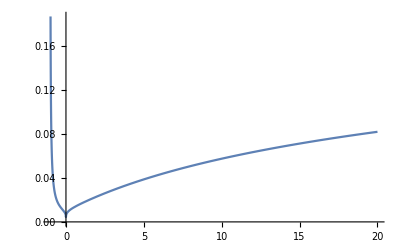

```mathematica
Plot[(ep[k,5])/(e[k,5]), {k,-0.99,20}]
```

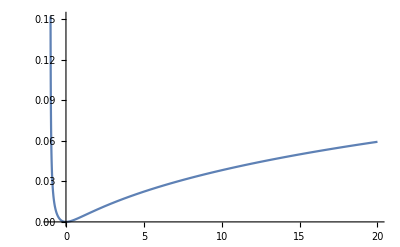

```mathematica
Plot[(ep[k,6])/(e[k,6]), {k,-0.99,20}]
```

```mathematica
ep[0,6]
```

0

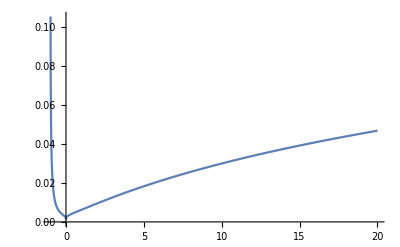

```mathematica
Plot[(ep[k,7])/(e[k,7]), {k,-0.99,20}]
```

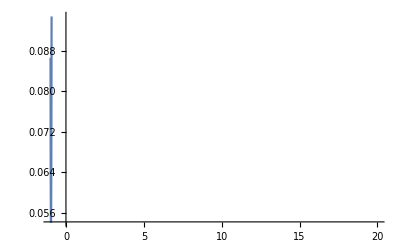

```mathematica
Plot[(ep[k,8])/(e[k,8]), {k,-0.99,20}]
```